1000

| Estimate | Standard Error | t-Statistic | P-Value
Ref | 6.78519 | 0.207804 | 32.6519 | 5.05837×10^-22

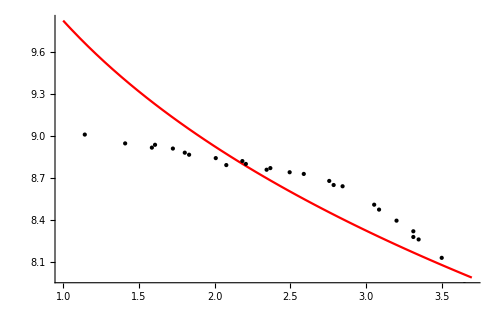

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["noyola_ready_0,25.dat"];
L=Length[data];
Ie=1000
(*Ref = 12*)
Ip[R_]:=Ie*Exp[-7.669*((R/Ref)^0.25-1.0)]
(*Plot[Log[Ip[R]],{R,0,12}]*)
fit = NonlinearModelFit[data,Log[Ip[R]],{Ref},R,MaxIterations->1000];
(*fit["BestFit"]*)
fit["ParameterTable"]
Plot[fit[R],{R,1,3.7},PlotStyle->Red,Epilog:>Point[data],ImageSize->500]
```